```mathematica
omegac=1000
```

1000

```mathematica
beta=10
```

10

```mathematica
Omega=2.0
```

2.

```mathematica
alpha=0.005
```

0.005

```mathematica
f[k_]=1/2*alpha*Exp[(-k/omegac)]*k*Coth[(beta*k/2)]/((k+Omega)*(k-Omega))
```

(0.0025 ⅇ^(-k/1000) k Coth[5 k])/((-2.+k) (2.+k))

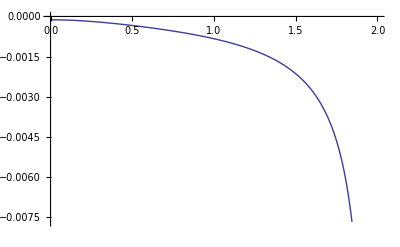

```mathematica
Plot[f[k],{k,0,2}]
```

```mathematica
NIntegrate[f[k],{k,0,Omega/2}]
```

-0.000380119

```mathematica
NIntegrate[f[k],{k,Omega/2,Omega-0.0001}] + NIntegrate[f[k],{k,Omega+0.0001,3*Omega/2}]
```

0.000634744

```mathematica
NIntegrate[f[k], {k, 3*Omega/2, Infinity}]
```

0.0138181

```mathematica
NIntegrate[f[k],{k,0.999,0.9999}]+NIntegrate[f[k],{k,1.0001,1.001}]
```

-1.49864×10^-6

```mathematica
NIntegrate[f[k],{k,0,Omega/2}] + NIntegrate[f[k],{k,Omega/2,Omega-0.0001}] + NIntegrate[f[k],{k,Omega+0.0001,3*Omega/2}] + NIntegrate[f[k], {k, 3*Omega/2, Infinity}]
```

0.0140727